# A Quantum-Like for the International Interaction Game

## The International Interaction Backward Induction Model

Explain here the Signorino  tree based model

## A Quantum-Like Approach

### Backward Induction Functions - Classical Setting

### Backward Induction Probability Functions - Quantum-Like Setting

```mathematica
(* for debugging *)
U1SQ=-0.23801; U1Acq2=1.025024; U1Acq1=-1.36844;U1Nego=-1.10122; U1War1=-1.51882; U1War2=-1.963;U1Cap1=-2.25679; U1Cap2=1.051597; U2SQ = -0.57593; U2Acq2 = -1.51157; U2Acq1=0.627684;U2Nego=0.591662; U2War1 = 0.808828; U2War2=0.817247;U2Cap1=0.861688; U2Cap2=-1.52841;
```

```mathematica
q10quantum[U2War1_,U2Cap2_]:=Sqrt[ⅇ^U2War1/(ⅇ^U2War1+ⅇ^U2Cap2)] ⅇ^(ⅈ Re[θ2]) ;
```

```mathematica
notq10quantum[U2War1_,U2Cap2_]:=  Sqrt[1-ⅇ^U2War1/(ⅇ^U2War1+ⅇ^U2Cap2)] ⅇ^(ⅈ Re[θ2]);
```

```mathematica
q11quantum[U2War1_,U2Cap2_]:=  q10quantum[U2War1,U2Cap2];
```

```mathematica
notq11quantum[U2War1_,U2Cap2_]:=  notq10quantum[U2War1,U2Cap2];
```

```mathematica
p8quantum[U1War2_,U1Cap1_] :=   Sqrt[ⅇ^U1War2/(ⅇ^U1War2+ⅇ^U1Cap1)] ⅇ^(ⅈ Re[θ1]);
```

```mathematica
notp8quantum[U1War2_,U1Cap1_]:= Sqrt[1-ⅇ^U1War2/(ⅇ^U1War2+ⅇ^U1Cap1)] ⅇ^(ⅈ Re[θ1]);
```

```mathematica
p12quantum[U1War2_,U1Cap1_]:= p8quantum[U1War2,U1Cap1];
```

```mathematica
notp12quantum[U1War2_,U1Cap1_]:= notp8quantum[U1War2,U1Cap1];
```

```mathematica
q9quantum[U1War2_,U1Cap1_,U2War2_,U2Cap1_, U2Nego_]:= Module[{UP2N12,p12, notp12},
p12=p12quantum[U1War2,U1Cap1];
notp12=notp12quantum[U1War2,U1Cap1];
UP2N12= p12 U2War2 + notp12 U2Cap1;
 Sqrt[ⅇ^UP2N12/(ⅇ^UP2N12+ⅇ^U2Nego)] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
notq9quantum[U1War2_,U1Cap1_,U2War2_,U2Cap1_, U2Nego_]:= Module[{UP2N12,p12, notp12},
p12=p12quantum[U1War2,U1Cap1];
notp12=notp12quantum[U1War2,U1Cap1];
UP2N12= p12 U2War2 + notp12 U2Cap1;
 Sqrt[1-ⅇ^UP2N12/(ⅇ^UP2N12+ⅇ^U2Nego)] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
p7quantum[U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_]:= Module[{UP1N11, q11, notq11},
q11 = q11quantum[U2War1,U2Cap2];
notq11=notq11quantum[U2War1,U2Cap2];
UP1N11=q11 U1War1+notq11 U1Cap2;
  Sqrt[ⅇ^UP1N11/(ⅇ^UP1N11+ⅇ^U1Nego)] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
notp7quantum[U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_]:= Module[{UP1N11, q11, notq11},
q11 = q11quantum[U2War1,U2Cap2];
notq11=notq11quantum[U2War1,U2Cap2];
UP1N11=q11 U1War1+notq11 U1Cap2;
  Sqrt[1-ⅇ^UP1N11/(ⅇ^UP1N11+ⅇ^U1Nego)] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
q6quantum[U1War1_, U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_]:= Module[{UP2N8,U2N11, UP2N7, p8,notp8,p7,notp7,q11,notq11},
p8=p8quantum[U1War2,U1Cap1];
notp8=notp8quantum[U1War2,U1Cap1];
notp7=notp7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
p7=p7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
UP2N8=p8 U2War2+notp8 U2Cap1;
q11=q11quantum[U2War1,U2Cap2];
notq11=notq11quantum[U2War1,U2Cap2];
U2N11=q11 U2War1+notq11 U2Cap2;
UP2N7=p7 U2N11+notp7 U2Nego;
  Sqrt[ⅇ^UP2N8/(ⅇ^UP2N8+ⅇ^UP2N7)] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
notq6quantum[U1War1_, U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_]:= Module[{UP2N8,U2N11, UP2N7, p8,notp8,p7,notp7,q11,notq11},
p8=p8quantum[U1War2,U1Cap1];
notp8=notp8quantum[U1War2,U1Cap1];
notp7=notp7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
p7=p7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
UP2N8=p8 U2War2+notp8 U2Cap1;
q11=q11quantum[U2War1,U2Cap2];
notq11=notq11quantum[U2War1,U2Cap2];
U2N11=q11 U2War1+notq11 U2Cap2;
UP2N7=p7 U2N11+notp7 U2Nego;
 Sqrt[1-ⅇ^UP2N8/(ⅇ^UP2N8+ⅇ^UP2N7)] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
p5quantum[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_, U1Nego_,U2Nego_]:=Module[{UP1N10,UP2N10,UP2N9,UP1N9,q10,notq10,q9,notq9,p12,notp12,UP1N12},
p12=p12quantum[U1War2,U1Cap1];
notp12=notp12quantum[U1War2,U1Cap1];
UP1N12=p12 U1War2 + notp12 U1Cap1;
q10=q10quantum[U2War1,U2Cap2];
notq10=notq10quantum[U2War1,U2Cap2];
q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
notq9=notq9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
UP1N10=q10 U1War1+notq10 U1Cap2;
UP1N9=q9 UP1N12+notq9 U1Nego;
 Sqrt[ⅇ^UP1N10/(ⅇ^UP1N10+ⅇ^UP1N9)] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
notp5quantum[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_, U1Nego_,U2Nego_]:=Module[{UP1N10,UP2N10,UP2N9,UP1N9,q10,notq10,q9,notq9,p12,notp12,UP1N12},
p12=p12quantum[U1War2,U1Cap1];
notp12=notp12quantum[U1War2,U1Cap1];
UP1N12=p12 U1War2 + notp12 U1Cap1;
q10=q10quantum[U2War1,U2Cap2];
notq10=notq10quantum[U2War1,U2Cap2];
q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
notq9=notq9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
UP1N10=q10 U1War1+notq10 U1Cap2;
UP1N9=q9 UP1N12+notq9 U1Nego;
Sqrt[1-ⅇ^UP1N10/(ⅇ^UP1N10+ⅇ^UP1N9)] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
p4quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_]:=Module[{UP1N6,q11,notq11,p8,notp8,p7,notp7,q6,notq6,UP1N11,UP1N8,UP1N7},
q11=q11quantum[U2War1,U2Cap2];
notq11=notp12quantum[U2War1,U2Cap2];

p8=p8quantum[U1War2,U1Cap1];
notp8 = notp8quantum[U1War2,U1Cap1];

p7=p7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
notp7=notp7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];

q6=q6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
notq6=notq6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

UP1N11=q11 U1War1+notq11 U1Cap2;
UP1N8=p8 U1War2+notp8 U1Cap1;
UP1N7=p7 UP1N11+notp7 U1Nego;
UP1N6=q6 UP1N8+notq6 UP1N7;
Sqrt[ⅇ^UP1N6/(ⅇ^UP1N6+ⅇ^U1Acq1)] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
notp4quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_]:=Module[{UP1N6,q11,notq11,p8,notp8,p7,notp7,q6,notq6,UP1N11,UP1N8,UP1N7},
q11=q11quantum[U2War1,U2Cap2];
notq11=notp12quantum[U2War1,U2Cap2];

p8=p8quantum[U1War2,U1Cap1];
notp8 = notp8quantum[U1War2,U1Cap1];

p7=p7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
notp7=notp7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];

q6=q6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
notq6=notq6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

UP1N11=q11 U1War1+notq11 U1Cap2;
UP1N8=p8 U1War2+notp8 U1Cap1;
UP1N7=p7 UP1N11+notp7 U1Nego;
UP1N6=q6 UP1N8+notq6 UP1N7;
Sqrt[1-ⅇ^UP1N6/(ⅇ^UP1N6+ⅇ^U1Acq1)] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
q3quantum[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_, U1Nego_,U2Nego_,U2Acq2_]:=Module[{UP2N12,UP2N10,UP2N9,UP2N5,p12,notp12,q10,notq10,q9,notq9,p5,notp5},
p12=p12quantum[U1War2,U1Cap1];
notp12=notp12quantum[U1War2,U1Cap1];
UP2N12=p12 U2War2 + notp12 U2Cap1;

q10=q10quantum[U2War1,U2Cap2];
notq10=notq10quantum[U2War1,U2Cap2];
UP2N10=q10 U2War1+notq10 U2Cap2;

q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
notq9=notq9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
UP2N9=q9 UP2N12+notq9 U2Nego;

p5=p5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];
notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];
UP2N5=p5 UP2N10+notp5 UP2N9;
Sqrt[ⅇ^UP2N5/(ⅇ^UP2N5+ⅇ^U2Acq2)] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
notq3quantum[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_, U1Nego_,U2Nego_,U2Acq2_]:=Module[{UP2N12,UP2N10,UP2N9,UP2N5,p12,notp12,q10,notq10,q9,notq9,p5,notp5},
p12=p12quantum[U1War2,U1Cap1];
notp12=notp12quantum[U1War2,U1Cap1];
UP2N12=p12 U2War2 + notp12 U2Cap1;

q10=q10quantum[U2War1,U2Cap2];
notq10=notq10quantum[U2War1,U2Cap2];
UP2N10=q10 U2War1+notq10 U2Cap2;

q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
notq9=notq9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
UP2N9=q9 UP2N12+notq9 U2Nego;

p5=p5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];
notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];
UP2N5=p5 UP2N10+notp5 UP2N9;
Sqrt[1-ⅇ^UP2N5/(ⅇ^UP2N5+ⅇ^U2Acq2)] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
q2quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_]:=Module[{UP2N4,q11,notq11,p7,notp7,p8,notp8,q6,notq6,p4,notp4,UP2N11,UP2N7,UP2N8,UP2N6},
q11=q11quantum[U2War1,U2Cap2];
notq11=notq11quantum[U2War1,U2Cap2];

p7=p7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
notp7=notp7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];

p8=p8quantum[U1War2,U1Cap1];
notp8=notp8quantum[U1War2,U1Cap1];

q6=q6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
notq6=notq6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];
notp4=notp4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

UP2N11=q11 U2War1+notq11 U2Cap2;
UP2N7=p7 UP2N11+notp7 U2Nego;
UP2N8=p8 U2War2+notp8 U2Cap1;
UP2N6= q6 UP2N8+notq6 UP2N7;
UP2N4=p4 UP2N6+notp4 U2Acq1;
Sqrt[ⅇ^UP2N4/(ⅇ^UP2N4+ⅇ^U2SQ)] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
notq2quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_]:=Module[{UP2N4,q11,notq11,p7,notp7,p8,notp8,q6,notq6,p4,notp4,UP2N11,UP2N7,UP2N8,UP2N6},
q11=q11quantum[U2War1,U2Cap2];
notq11=notq11quantum[U2War1,U2Cap2];

p7=p7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
notp7=notp7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];

p8=p8quantum[U1War2,U1Cap1];
notp8=notp8quantum[U1War2,U1Cap1];

q6=q6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
notq6=notq6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];
notp4=notp4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

UP2N11=q11 U2War1+notq11 U2Cap2;
UP2N7=p7 UP2N11+notp7 U2Nego;
UP2N8=p8 U2War2+notp8 U2Cap1;
UP2N6= q6 UP2N8+notq6 UP2N7;
UP2N4=p4 UP2N6+notp4 U2Acq1;
Sqrt[1-ⅇ^UP2N4/(ⅇ^UP2N4+ⅇ^U2SQ)] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
p1quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=Module[{UP1N2,UP1N3,UP1N4,UP1N5,UP1N6,UP1N9,UP1N10,UP1N12,q2,notq2,q3,notq3,p4,notp4,p5,notp5,q6,notq6,p8,notp8,p7,notp7,q9,notq9,q10,notq10,q11,notq11,p12,notp12, UP1N11,UP1N7,UP1N8},

p12=p12quantum[U1War2,U1Cap1];
notp12=notp12quantum[U1War2,U1Cap1];
p8=p8quantum[U1War2,U1Cap1];
notp8=notp8quantum[U1War2,U1Cap1];
q11=q11quantum[U2War1,U2Cap2];
notq11=notq11quantum[U2War1,U2Cap2];

q10=q10quantum[U2War1,U2Cap2];
notq10=notp12quantum[U2War1,U2Cap2];

q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
notq9=notq9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];

p7=p7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
notp7=notp7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];

q6=q6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
notq6=notq6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

p5 =p5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];
notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];
notp4=notp4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

q3=q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];
notq3=notq3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];
notq2=notq2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

UP1N12=p12 U1War1+notp12 U1Cap1;
UP1N11=q11 U1War1+notq11 U1Cap2;
UP1N9=q9 UP1N12+notq9 U1Nego;

UP1N7=p7 UP1N11+notp7 U1Nego;
UP1N8=p8 U2War2+notp8 U2Cap1;

UP1N10=q10 U1War1+notq10 U1Cap2;
UP1N6= q6 UP1N8+notq6 UP1N7;

UP1N5=p5 UP1N10+notp5 UP1N9;
UP1N4=p4 UP1N6+notp4 U1Acq1;

UP1N3=q3 UP1N5+notq3 U1Acq2;
UP1N2=q2 UP1N4+notq2 U1SQ;
Sqrt[ⅇ^UP1N3/(ⅇ^UP1N3+ⅇ^UP1N2)] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
notp1quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=Module[{UP1N2,UP1N3,UP1N4,UP1N5,UP1N6,UP1N9,UP1N10,UP1N12,q2,notq2,q3,notq3,p4,notp4,p5,notp5,q6,notq6,p8,notp8,p7,notp7,q9,notq9,q10,notq10,q11,notq11,p12,notp12, UP1N11,UP1N7,UP1N8},

p12=p12quantum[U1War2,U1Cap1];
notp12=notp12quantum[U1War2,U1Cap1];

q11=q11quantum[U2War1,U2Cap2];
notq11=notq11quantum[U2War1,U2Cap2];

q10=q10quantum[U2War1,U2Cap2];
notq10=notp12quantum[U2War1,U2Cap2];
p8=p8quantum[U1War2,U1Cap1];
notp8=notp8quantum[U1War2,U1Cap1];
q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
notq9=notq9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];

p7=p7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
notp7=notp7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];

q6=q6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
notq6=notq6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

p5 =p5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];
notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];
notp4=notp4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

q3=q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];
notq3=notq3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];
notq2=notq2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

UP1N12=p12 U1War1+notp12 U1Cap1;
UP1N11=q11 U1War1+notq11 U1Cap2;
UP1N9=q9 UP1N12+notq9 U1Nego;

UP1N7=p7 UP1N11+notp7 U1Nego;
UP1N8=p8 U2War2+notp8 U2Cap1;

UP1N10=q10 U1War1+notq10 U1Cap2;
UP1N6= q6 UP1N8+notq6 UP1N7;

UP1N5=p5 UP1N10+notp5 UP1N9;
UP1N4=p4 UP1N6+notp4 U1Acq1;

UP1N3=q3 UP1N5+notq3 U1Acq2;
UP1N2=q2 UP1N4+notq2 U1SQ;
Sqrt[1-ⅇ^UP1N3/(ⅇ^UP1N3+ⅇ^UP1N2)] ⅇ^(ⅈ Re[θ1])
];
```

### Backward Induction Outcome Functions - Quantum-Like Setting

```mathematica
SQquantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:= Module[{term1,conjugate,notp1,notq2},

notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

notq2=notq2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

term1= notp1 notq2;
conjugate=Conjugate[term1];
term1 conjugate
];
```

```mathematica
ACQ1quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=Module[{notp1,q2,notq2,notp4,term1,conjugate},
notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

notp4=notp4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

term1= notp1 q2 notp4 ;
conjugate=Conjugate[term1];
term1 conjugate
];
```

```mathematica
ACQ2quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=Module[{p1,notq3,term1,conjugate},
p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

notq3=notq3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

term1= p1 notq3;
conjugate=Conjugate[term1];
term1 conjugate
];
```

```mathematica
(* ACQ2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ] *)
```

```mathematica
(* ------------- Probability for Negotiation --------------------------- *)
```

```mathematica
NEGOquantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=Module[{p1,notp1,q2,q3,p4,notp5,notq6,notp7,notq9,term1, conjugate},
p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];
notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

q3 =q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

notq6=notq6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

notp7=notp7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
notq9=notq9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];

(* ((1-p1) q2 p4 (1-q6) (1-p7) + p1 q3 (1-p5) (1-q9)) *)
term1=notp1 q2 p4 notq6 notp7 +p1 q3 notp5 notq9;
conjugate=Conjugate[term1];
term1 conjugate
];
```

```mathematica
(* ------------- Probability for CAP 1 ---------------------------------- *)
```

```mathematica
CAP1quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=Module[{notp1,p1,q2,p4,q6,notp8,q3,notp5,q9,notp12,term1, conjugate},

notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

q6=q6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

notp8=notp8quantum[U1War2,U1Cap1];

p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q3 =q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];

notp12=notp12quantum[U1War2,U1Cap1];

term1= notp1 q2 p4 q6 notp8 + p1 q3 notp5 q9 notp12;
conjugate=Conjugate[term1];
 term1 conjugate
];
```

```mathematica
(* ------------- Probability for CAP 2 ---------------------------------- *)
```

```mathematica
CAP2quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=Module[{notp1,q2,p1,p4,notq6,q6,p7,notp8,q3,notp5,q9,notp12,notq11,term1, conjugate, p5, notq10},

notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

notq6=notq6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

p7=p7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];

notp8=notp8quantum[U1War2,U1Cap1];

p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q3 =q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

p5=p5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];

notp12=notp12quantum[U1War2,U1Cap1];

notq11=notq11quantum[U2War1,U2Cap2];

notq10=notq10quantum[U2War1,U2Cap2];

term1= notp1 q2 p4 notq6 p7 notq11 + p1 q3 p5 notq10;
conjugate=Conjugate[term1];
 term1 conjugate
];
```

```mathematica
(* ------------- Probability for WAR 1 ---------------------------------- *)
```

```mathematica
WAR1quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_] := Module[{notp1,p1, q2, p4,notq6, p7,q11,q3,q10, p5, term1, conjugate},

notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

notq6=notq6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

p7=p7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];

q11=q11quantum[U2War1,U2Cap2];

q3 =q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

q10=q10quantum[U2War1,U2Cap2];

p5=p5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

(* ((1-p1)q2 p4 (1-q6) p7 q11 + p1 q3 p5 q10  )  *)
term1 = notp1 q2 p4 notq6 p7 q11 + p1 q3 p5 q10;
conjugate = Conjugate[term1];
 term1 conjugate
];
```

```mathematica
(* ------------- Probability for WAR 2 ---------------------------------- *)
```

```mathematica
WAR2quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_] := Module[{notp1,p1, q2, p4,q6,q11,p8,q3,q10, notp5, q9,p12,term1, conjugate},

notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

q6=q6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

q11=q11quantum[U2War1,U2Cap2];

p8=p8quantum[U1War2,U1Cap1];

q3 =q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

q10=q10quantum[U2War1,U2Cap2];

notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];

p12=p12quantum[U1War2,U1Cap1];

(* (((1-p1) q2 p4 q6 p8 + p1 q3 (1-p5) q9 p12)  *)
term1 = notp1 q2 p4 q6 p8  + p1 q3 notp5 q9 p12;
conjugate = Conjugate[term1];
 term1 conjugate
];
```

### Visualisation

```mathematica
makeplot[Outcome_, x_,y_,title_]:= Plot3D[Re[Outcome],{θ1,0, 2 π},{θ2,0, 2 π},PlotRange->All,ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style["θ_Player1",16],Style["θ_Player2",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],PlotLabel->title]
```

### The Dataset

```mathematica
data = Import["/Users/162191/Desktop/utilities.csv"];
```

```mathematica
numCols = Length[data[[1]]]
```

20

```mathematica
numRows=Length[data]
```

499

```mathematica
INTEVX=0;
INTEVY = 2 π;
```

```mathematica
(* Dataset row *)
```

```mathematica
i=3;

Clear[θ1,θ2];
(* Player ID *)
Player1=data[[i,1]];
Player2=data[[i,2]];

Print["Loading Player ", Player1," and ", Player2];

(* Utilities for Player 1 *)
U1SQ = data[[i,3]];
U1Acq1 = data[[i,4]];
U1Acq2=data[[i,5]];
U1Nego=data[[i,6]];
U1Cap1=data[[i,7]];
U1Cap2=data[[i,8]];
U1War1=data[[i,9]];
U1War2=data[[i,10]];

(* Player 2 utilities *)
U2SQ = data[[i,11]];
U2Acq2 = data[[i,12]];
U2Acq1=data[[i,13]];
U2Nego=data[[i,14]];
U2Cap2=data[[i,15]];
U2Cap1=data[[i,16]];
U2War2=data[[i,17]];
U2War1=data[[i,18]];

(* Groundtruth *)
Grountruth=data[[i,20]];
Print["Groundtruth: ", Grountruth];

(* Compute Quantum Probabilities for Different Outcomes *)
Print["Computing probabilities"]
SQ = SQquantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];
ACQ1 = ACQ1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];
ACQ2=ACQ2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];
NEGO=NEGOquantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];
CAP1=CAP1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];
CAP2=CAP2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];
WAR1=WAR1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ] ;
WAR2 = WAR2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ] ;
```

Loading Player RUS and TUR

Groundtruth: Nego

Computing probabilities

```mathematica
Print["Normalizing probabilities"]
SQnorm = SQ / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2);
ACQ1norm = ACQ1 / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2);
ACQ2norm = ACQ2 / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2);
NEGOnorm = NEGO / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2);
CAP1norm = CAP1 / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2);
CAP2norm = CAP2 / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2);
WAR1norm = WAR1 / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2);
WAR2norm = WAR2 / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2);
```

Normalizing probabilities

```mathematica
makeplot[SQnorm, INTEVX,INTEVY,"Probability Space for Status QUO" ]
```

-Graphics3D-

```mathematica
makeplot[ACQ1norm, INTEVX,INTEVY,"Probability Space for ACQ1" ]
```

-Graphics3D-

```mathematica
makeplot[ACQ2norm, INTEVX,INTEVY,"Probability Space for ACQ2" ]
```

-Graphics3D-

```mathematica
makeplot[CAP1norm, INTEVX,INTEVY,"Probability Space for CAP1" ]
```

-Graphics3D-

```mathematica
makeplot[CAP2norm, INTEVX,INTEVY,"Probability Space for CAP2" ]
```

-Graphics3D-

```mathematica
makeplot[NEGOnorm, INTEVX,INTEVY,"Probability Space for NEGO" ]
```

-Graphics3D-

```mathematica
makeplot[WAR1norm, INTEVX,INTEVY,"Probability Space for WAR1" ]
```

-Graphics3D-

```mathematica
makeplot[WAR2norm, INTEVX,INTEVY,"Probability Space for WAR2" ]
```

-Graphics3D-

```mathematica
out = TimeConstrained[ FindInstance[{Re[CAP2norm]≥ Re[ SQnorm], Re[CAP2norm]≥ Re[ACQ1norm], Re[CAP2norm]≥ Re[ACQ2norm], Re[CAP2norm]≥ Re[CAP1norm],   Re[CAP2norm]≥ Re[NEGOnorm],  Re[CAP2norm]≥ Re[WAR1norm] , Re[CAP2norm]≥ Re[WAR2norm] }, {θ1, θ2}, Reals],5];
```

FindInstance::nddc: The system Re[Divide[(0.565062 <<3>> Power[Divide[Power[E, 1.92768 <<1>> Power[<<2>>] + <<1>>], <<1>>], <<1>>] + 0.565062 <<6>>) <<1>>, <<1>>]] >= Re[<<1>>] && <<6>> contains a nonreal constant 2 ⅈ. With the domain  specified, all constants should be real.

General::stop: Further output of FindInstance::nddc will be suppressed during this calculation.

```mathematica
out
```

FindInstance::nddc: The system Re[Divide[(0.565062 <<3>> Power[Divide[Power[E, 1.92768 <<1>> Power[<<2>>] + <<1>>], <<1>>], <<1>>] + 0.565062 <<6>>) <<1>>, <<1>>]] >= Re[<<1>>] && <<6>> contains a nonreal constant 2 ⅈ. With the domain  specified, all constants should be real.

1
 |  |  |  |

```mathematica
(* CAP2 overtakes all *)
RegionPlot[{CAP2norm≥  SQnorm && CAP2norm≥ ACQ1norm && CAP2norm≥ ACQ2norm&& CAP2norm≥ CAP1norm &&  CAP2norm≥ NEGOnorm&&  CAP2norm≥ WAR1norm && CAP2norm≥ WAR2norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
(* CAP1 overtakes all *)
RegionPlot[{CAP1norm≥  SQnorm && CAP1norm≥ ACQ1norm && CAP1norm≥ ACQ2norm&& CAP1norm≥ CAP2norm &&  CAP1norm≥ NEGOnorm&&  CAP1norm≥ WAR1norm && CAP1norm≥ WAR2norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

-Graphics-

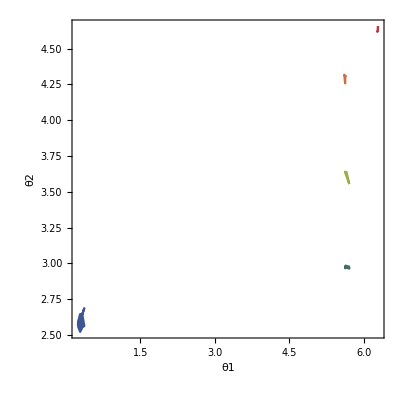

```mathematica
(* NEGO overtakes all *)
RegionPlot[{NEGOnorm≥  SQnorm && NEGOnorm≥ ACQ1norm && NEGOnorm≥ ACQ2norm&& NEGOnorm≥ CAP2norm &&  NEGOnorm≥ CAP1norm&&  NEGOnorm≥ WAR1norm && NEGOnorm≥ WAR2norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

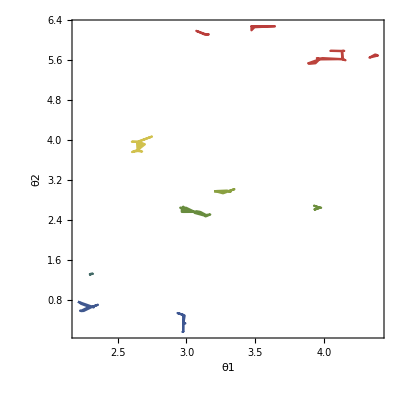

```mathematica
(* SQ overtakes all *)
RegionPlot[{SQnorm≥  NEGOnorm && SQnorm≥ ACQ1norm && SQnorm≥ ACQ2norm&& SQnorm≥ CAP2norm &&  SQnorm≥ CAP1norm&&  SQnorm≥ WAR1norm && SQnorm≥ WAR2norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

```mathematica
(* ACQ1 overtakes all *)
RegionPlot[{ACQ1norm≥  NEGOnorm && ACQ1norm≥ SQnorm && ACQ1norm≥ ACQ2norm&& ACQ1norm≥ CAP2norm &&  ACQ1norm≥ CAP1norm&&  ACQ1norm≥ WAR1norm && ACQ1norm≥ WAR2norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

-Graphics-

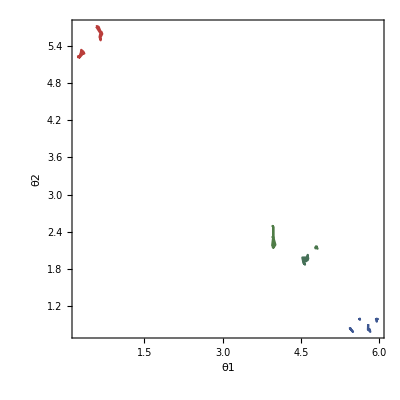

```mathematica
(* ACQ2 overtakes all *)
RegionPlot[{ACQ2norm≥  NEGOnorm && ACQ2norm≥ SQnorm && ACQ2norm≥ ACQ1norm&& ACQ2norm≥ CAP2norm &&  ACQ2norm≥ CAP1norm&&  ACQ2norm≥ WAR1norm && ACQ2norm≥ WAR2norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

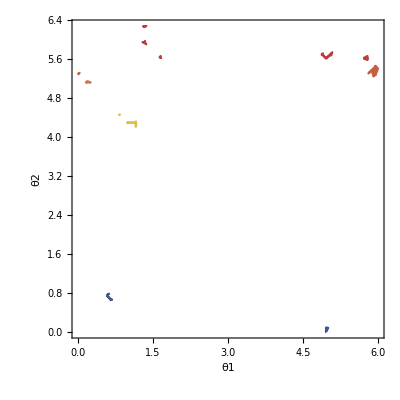

```mathematica
(* WAR1 overtakes all *)
RegionPlot[{WAR1norm≥  NEGOnorm && WAR1norm≥ SQnorm && WAR1norm≥ ACQ1norm&& WAR1norm≥ CAP2norm &&  WAR1norm≥ CAP1norm&&  WAR1norm ≥ ACQ2norm && WAR1norm≥ WAR2norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

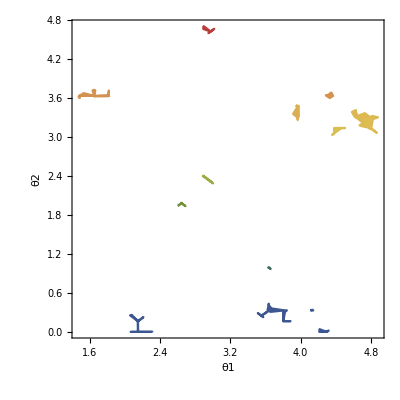

```mathematica
(* WAR2 overtakes all *)
RegionPlot[{WAR2norm≥  NEGOnorm && WAR2norm≥ SQnorm && WAR2norm≥ ACQ1norm&& WAR2norm≥ CAP2norm &&  WAR2norm≥ CAP1norm&&  WAR2norm ≥ ACQ2norm && WAR2norm≥ WAR1norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

```mathematica
(* Check min, max, and classical probabilities *)
```

```mathematica
θ1=π;
θ2=π;
{SQnorm,ACQ1norm,ACQ2norm,NEGOnorm,CAP1norm,CAP2norm,WAR1norm,WAR2norm}
```

{0.278487,0.184394,0.196569,0.000267477,0.0614346,0.0527825,0.112527,0.113539}

```mathematica
θ1=0;
θ2=0;
{SQnorm,ACQ1norm,ACQ2norm,NEGOnorm,CAP1norm,CAP2norm,WAR1norm,WAR2norm}
```

{0.0539847,0.0506535,0.535274,0.0376138,0.0271691,0.0782571,0.166836,0.0502119}

```mathematica
θ1=π/2;
θ2=π/2;
{Re[SQnorm],Re[ACQ1norm],Re[ACQ2norm],Re[NEGOnorm],Re[CAP1norm],Re[CAP2norm],Re[WAR1norm],Re[WAR2norm]}
```

{0.542278,0.0308122,0.0123163,0.12386,0.0971734,0.0044611,0.00951062,0.179589}